# 1D

```mathematica
normalized[func_,x_]:=func[x]-NIntegrate[func[y],{y,0,1}]
periodized[func_,x_]:=func[x]-x func[1]-(1-x)func[0]
```

## Polynomial

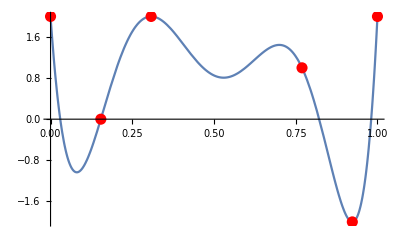

```mathematica
ptsSym={{0,2},{2/13,0},{4/13,2,0},{10/13,1},{12/13,-2,0},{1,2}};
pts=ptsSym//N;

f[x_]=InterpolatingPolynomial[pts,x];

Plot[f[x],{x,0,1},PlotRange->All,Epilog->{Red,PointSize[0.02],Point@pts[[All, ;;2]]}]
```

```mathematica
ClearAll[g,d,e,ϕ]
g[x_]:=normalized[f,x];
d[n_,x_]:=normalized[g[#]^n&,x];
etemp[n_,x_]:=Integrate[d[n,x],x];
ϕtemp[n_,x_]:=-Integrate[etemp[n,x],x];
ϕ[n_,x_]:=periodized[Evaluate@ϕtemp[n,#]&,x];
e[n_,x_]:=-D[ϕ[n,x],x];
```

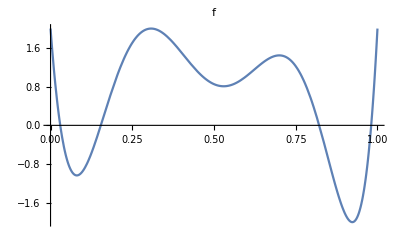

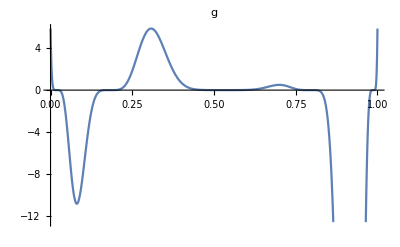

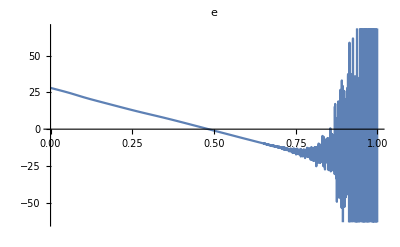

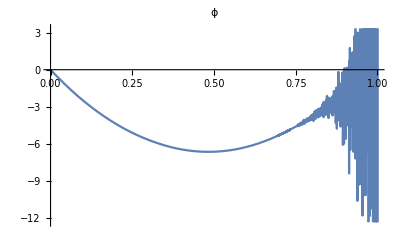

```mathematica
nn=5;

Plot[f[x],{x,0,1},PlotLabel->"f"]
Plot[Evaluate@d[nn,x],{x,0,1},PlotLabel->"g"]
Plot[Evaluate@e[nn,x],{x,0,1},PlotLabel->"e"]

fm = FindMaximum[ϕ[nn,x],{x,0,1}];
{ϕmax,xmax} = {fm[[1]],x/.fm[[2]]};
Show[Plot[Evaluate@ϕ[nn,x],{x,0,1},PlotLabel->"ϕ"],ListPlot[{{xmax,ϕmax},{xmax,0}},PlotMarkers->"*",PlotStyle->{Red,Thick}]]
```

## Rational

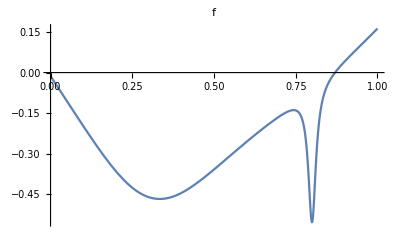

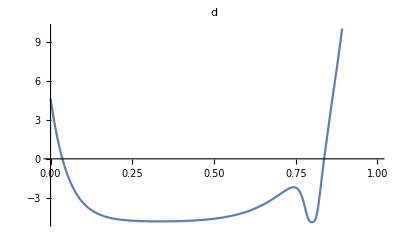

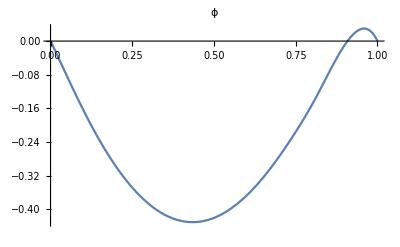

```mathematica
nn=10;

f[x_]:=(x-0.5)^2-0.5/(10(x-0.3)^2+1)-10^-4/((x-0.8)^2+0.2 10^-3);
g[x_]:=normalized[f,x];
d[n_,x_]:=normalized[Exp[n g[#]]&,x];
ϕ=Module[{phi},phi/.NDSolve[{phi''[x]==-d[nn,x],phi[0]==0,phi[1]==0},phi,{x,0,1}]][[1]];

Plot[f[x],{x,0,1},PlotLabel->"f"]
Plot[Evaluate@d[nn,x],{x,0,1},PlotLabel->"d"]
Plot[ϕ[x],{x,0,1},PlotLabel->"ϕ"]
```

# 2D

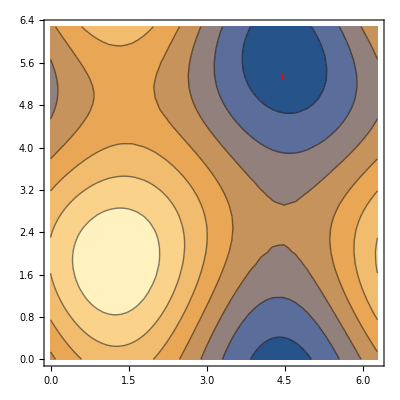

```mathematica
SeedRandom[10];
r=ArrayReshape[RandomReal[{0,1},9,WorkingPrecision->20],{3,3}];
loss[x_,y_]:=Sum[r[[i+1,j+1]] Cos[x/2]^i Sin[x/2]^(2-i)Cos[y/2]^j Sin[y/2]^(2-j),{i,0,2},{j,0,2}]
monoloss[x_,y_]:=Coefficient[(loss[x,y]//FullSimplify)/.{Cos[v_]:>t Cos[v],Sin[v_]:>t Sin[v]},t]
minGuess=Mod[Module[{x,y},{x,y}/.FindMinimum[monoloss[x,y],{x,y},WorkingPrecision->20][[2]]],2π]//N;

Show[ContourPlot[loss[x,y],{x,0,2π},{y,0,2π}],ListPlot[{minGuess},PlotStyle->{Thick,Red},PlotMarkers->"*"]]
```

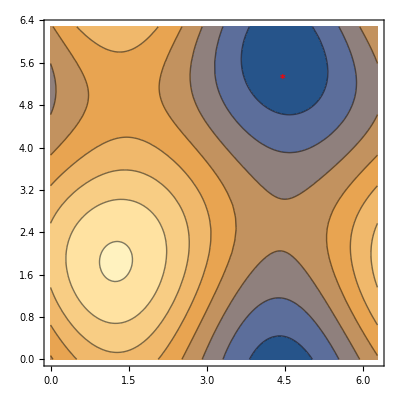

```mathematica
Show[ContourPlot[stryLinv[20],{x,0,2π},{y,0,2π}],ListPlot[{minGuess},PlotStyle->{Thick,Red},PlotMarkers->"*"]]
```

```mathematica
stry=loss[x,y]-0.57769716785875164073476113374456854271`17.74118302113632//FullSimplify//Chop
```

Cos[y] (-0.16226355268402+0.0577582712199865 Sin[x])+Cos[x] (0.105977858490373+0.033933886247093 Cos[y]+0.0613639578132058 Sin[y])+Sin[x] (0.4208521518140327+0.07814924749614423 Sin[y])+0.248287332003948 Sin[y]

```mathematica
stryLinv[n_]:=2^n(-1)^n stry/.{Cos[v_]:>Cos[v]/2^n,Sin[v_]:>Sin[v]/2^n}
```

```mathematica
Laplacian[stryLinv[1],{x,y}]- stry//Simplify//Chop
Laplacian[Laplacian[stryLinv[2],{x,y}],{x,y}]-stry//Simplify//Chop
Laplacian[Laplacian[Laplacian[stryLinv[3],{x,y}],{x,y}],{x,y}]-stry//Simplify//Chop
```

0

0

0

```mathematica
stryLinv[30]//N//Chop//Expand
```

0.105978 Cos[x]-0.162264 Cos[y]+0.420852 Sin[x]+0.248287 Sin[y]

```mathematica
monoloss[x,y]//Chop
```

0.1059778584903725 Cos[x]-0.16226355268402018 Cos[y]+0.42085215181403273 Sin[x]+0.24828733200394796 Sin[y]